```mathematica
<<NFPackages`structuralMechanicsBook` // Quiet
```

## How to think about intermediate column

-Graphics- | " ⟶_(focus on\n
 column FJ) " |  | " ⟶_(focus on\n
 node J) " | 
"(a)" | "" | "(b)" | "" | "(c)"

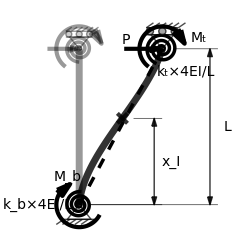

## Demo

## Sidesway formulas

### One story

k_sh  = Piecewise[{{(4 k)/(3+4 k) (3 EI)/L^3, hinge support        (a)}, {(1+4 k)/(4+4k)(12 EI)/L^3, fixed support        (b)}, {0, roller support        (c)}}]

(M_(inner top)

M_(inner bottom))  = ((2k)/(1+4k)
-(1+2k)/(1+4k)) V L	   (fixed end)

(M_(inner top)

M_(inner bottom))  = (1

0) V L	  	 (hinged end)

x_I  = (1+2k)/(1+4k) L				(fixed end)

### First iteration

-Graphics-

### Second iteration

-Graphics-

## Example - 3-story building

-Graphics-      -Graphics-

```mathematica
kb = 2.914;
kt = 1.286;
EI = 1.5;
L = 3;
V = 6.692;
Mb = 9.051;
Mt = 3.498;
ksh[ kb, kt, EI, L, V, Mb, Mt ]
```

0.296205

-Graphics--Graphics-
-Graphics-

-Graphics--Graphics-

-Graphics-

```mathematica
ksh[ kb_, kt_, EI_, L_ ] := (kb + kt + 4 kb kt)/(3 + 4 kb + 4 kt + 4kb kt) 12 EI/L^3
```

```mathematica
ksh[ kb_, kt_, EI_, L_, V_, Mb_, Mt_ ] := (kb + kt + 4 kb kt)/(3 + 4 kb + 4 kt + 4 kb kt + 3 (1+ 2kt) (Mb / (V L)) + 3 (1+ 2kb) (Mt / (V L))) 12 EI/L^3
```

#### Formula for shear stiffness

```mathematica
ksh[ kb_, kt_, EI_, L_, V_, Mb_, Mt_ ] := (kb + kt + 4 kb kt)/(3 + 4 kb + 4 kt + 4 kb kt + 3 (1+ 2kt) (Mb / (V L)) + 3 (1+ 2kb) (Mt / (V L))) 12 EI/L^3
```

```mathematica
MtopAndBottom[ kb_, kt_, Mb_, Mt_, V_, EI_, L_] := {(kt + 2 kb kt)/(kb + kt + 4 kb kt),- (kb + 2 kb kt)/(kb + kt + 4 kb kt)} V L  + {kt/(kb + kt + 4 kb kt), kt/(kb + kt + 4 kb kt)}Mb - {kb/(kb + kt + 4 kb kt), kb/(kb + kt + 4 kb kt)}Mt
```

#### Details

```mathematica
kt = 1.286;
kb = 2.914;
L = 3;
EI = 1.5;
V = 6.692;
Mb = 9.051;
Mt = 3.498;
ksh[ kb, kt, Mb, Mt, V, EI, L ]
```

0.296205